## Integrations

```mathematica
Sum[(r0/R)^j*Cos[j*(θ-theta0)]/(1+j/(q*R)),{j,1,Infinity}]
```

1/(2 (1+q R))ⅇ^(-ⅈ theta0-ⅈ θ) q r0 (ⅇ^(2 ⅈ theta0) Hypergeometric2F1[1,1+q R,2+q R,(ⅇ^(ⅈ theta0-ⅈ θ) r0)/R]+ⅇ^(2 ⅈ θ) Hypergeometric2F1[1,1+q R,2+q R,(ⅇ^(-ⅈ theta0+ⅈ θ) r0)/R])

```mathematica
Integrate[1/(2π R)*(1+2*Sum[(r0/R)^j*Cos[j*(θ-theta0)]/(1+j/(q*R)),{j,1,Infinity}]),{θ,(2π)/N*(k-1),(2π)/N*k}]
```

∫_((2 (-1+k) π)/N)^((2 k π)/N) 1/(2 π R)(1+1/(1+q R)ⅇ^(-ⅈ theta0-ⅈ θ) q r0 (ⅇ^(2 ⅈ theta0) Hypergeometric2F1[1,1+q R,2+q R,(ⅇ^(ⅈ theta0-ⅈ θ) r0)/R]+ⅇ^(2 ⅈ θ) Hypergeometric2F1[1,1+q R,2+q R,(ⅇ^(-ⅈ theta0+ⅈ θ) r0)/R]))ⅆθ

```mathematica
Integrate[1/(2π R)*(2*(r0/R)^j*Cos[j*(θ-theta0)]/(1+j/(q*R))),{θ,(2π)/N*(k-1),(2π)/N*k}]
```

(2 q (r0/R)^j Cos[(j (π-2 k π+N theta0))/N] Sin[(j π)/N])/(j^2 π+j π q R)

## Define pbb

```mathematica
pk2[r0_,theta0_,k_,q_,R_,N_]:=1/(N * R)+ Sum[(2 q (r0/R)^j Cos[(j (π-2 k π+N theta0))/N] Sin[(j π)/N])/(j^2 π+j π q R),{j,1,Infinity}]
```

```mathematica
N[pk2[0.1,0,5,10,1.0,60]]
```

0.0195315-2.11133×10^-17 ⅈ

```mathematica
pk[r0_,theta0_,k_,q_,R_,N_]:=1/(π R)*(π/N+Sum[(r0/R)^j*1/(1/j+1/(q*R))(Sin[j*((2π*k)/N-theta0)]-Sin[j*((2π)/N(k-1)-theta0)]),{j,1,Infinity}])
```

```mathematica
N[pk[0.1,0,5,10,1.0,60]]
```

0.0200364-9.09708×10^-6 ⅈ

```mathematica
pk[0.9,0,2,10,1.0,60]
pk2[0.9,0,2,10,1.0,60]
```

-3.27484-3.799×10^-13 ⅈ

0.100032+1.44777×10^-16 ⅈ

## Figures

### q = 10

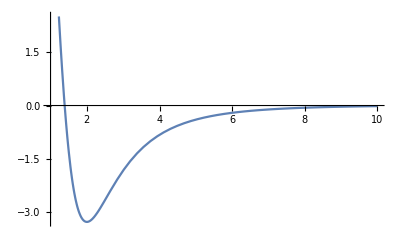

```mathematica
Plot[Re[pk[0.9,0,k,10,1.0,60]],{k,1,10}]
```

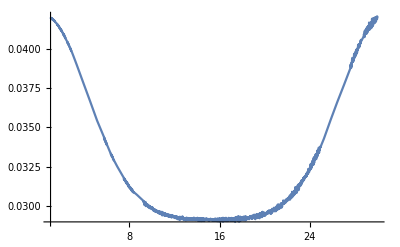

```mathematica
Plot[Re[pk[0.1,0,k,10,1.0,30]],{k,1,30}]
```

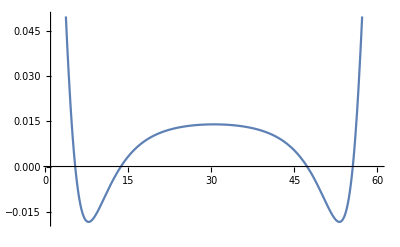

```mathematica
Plot[Re[pk[0.5,0,k,10,1.0,60]],{k,1,60}]
```

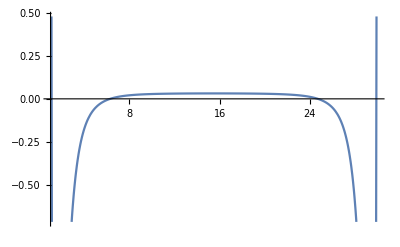

```mathematica
Plot[Re[pk[0.9,0,k,10,1.0,30]],{k,1,30}]
```

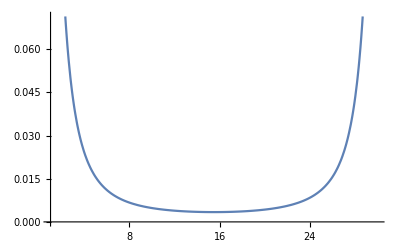

```mathematica
Plot[Re[pk2[0.9,0,k,10,1.0,30]],{k,1,30}]
```

### q = 1

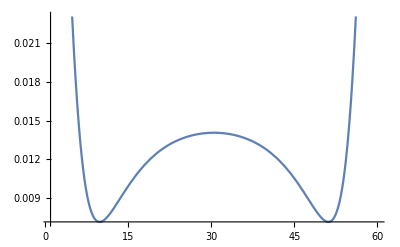

```mathematica
Plot[Re[pk[0.5,0,k,1,1.0,60]],{k,1,60}]
```

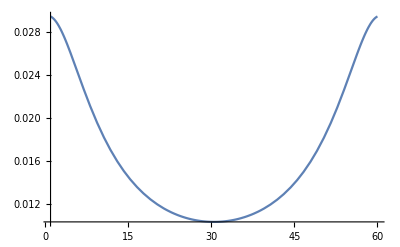

```mathematica
Plot[Re[pk2[0.5,0,k,1,1.0,60]],{k,1,60}]
```

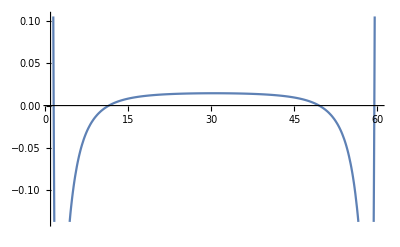

```mathematica
Plot[Re[pk[0.9,0,k,1,1.0,60]],{k,1,60}]
```

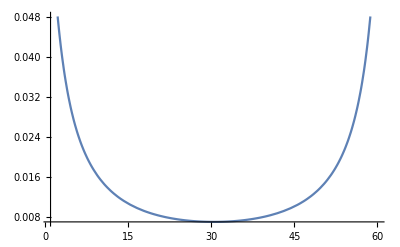

```mathematica
Plot[Re[pk2[0.9,0,k,1,1.0,60]],{k,1,60}]
```